```mathematica
ClearAll["Global`*"]
```

```mathematica
norm[θ_]:=θ-2π Floor[θ/(2π)]
```

```mathematica
(*check U*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/U_n_12_10.csv"][[2;;]];
t=Table[{t[[i,3]],t[[i,1]],t[[i,2]]},{i,2,Length[t]}]
```

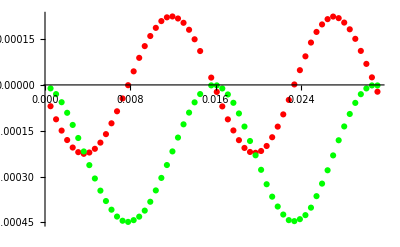

```mathematica
Show[ListPlot[Table[{t[[i,1]],t[[i,2]]},{i,1,Length[t]}],PlotStyle->Red],ListPlot[Table[{t[[i,1]],t[[i,3]]},{i,1,Length[t]}],PlotStyle->Green],PlotRange->Full]
```

```mathematica
(*check nu*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/nu_n_12_10.csv"][[2;;]];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{0.0291076,1.04248},{0.0301472,1.02028},{0.0270285,1.07919},{0.0280681,1.05601},{0.0249494,1.1054},{0.025989,1.08369},{0.0228703,1.10871},{0.0239098,1.09728},{0.0207912,1.09241},{0.0218307,1.09349},{0.0187121,1.06166},{0.0197516,1.07213},{0.0166329,1.02288},{0.0176725,1.0383},{0.0145538,0.983644},{0.0155934,1.00178},{0.0124747,0.951137},{0.0135143,0.967809},{0.0103956,0.92713},{0.0114351,0.941772},{0.00831647,0.916434},{0.00935603,0.927916},{0.00623735,0.921467},{0.00727691,0.923966},{0.00415823,0.938368},{0.00519779,0.932424},{0.00207912,0.965983},{0.00311868,0.953463},{0.,1.0028},{0.00103956,0.983962}}

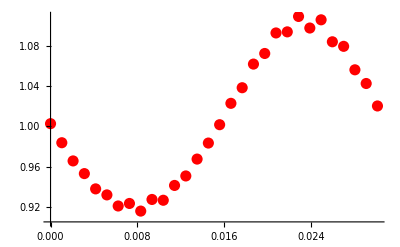

```mathematica
plotnumν=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```

```mathematica
(*check psi*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/dpsi_n_12_10.csv"][[2;;]];
t=Table[{t[[i,2]],norm[t[[i,1]]]},{i,2,Length[t]}]
```

{{0.0291076,4.62539},{0.0301472,4.62661},{0.0270285,4.64725},{0.0280681,4.63898},{0.0249494,4.68101},{0.025989,4.66532},{0.0228703,4.72156},{0.0239098,4.70392},{0.0207912,4.76107},{0.0218307,4.74144},{0.0187121,4.79197},{0.0197516,4.77365},{0.0166329,4.80336},{0.0176725,4.7938},{0.0145538,4.80106},{0.0155934,4.80088},{0.0124747,4.78415},{0.0135143,4.79076},{0.0103956,4.75953},{0.0114351,4.76772},{0.00831647,4.72054},{0.00935603,4.73744},{0.00623735,4.68508},{0.00727691,4.70385},{0.00415823,4.65516},{0.00519779,4.67123},{0.00207912,4.62978},{0.00311868,4.64385},{0.,4.61865},{0.00103956,4.62651}}

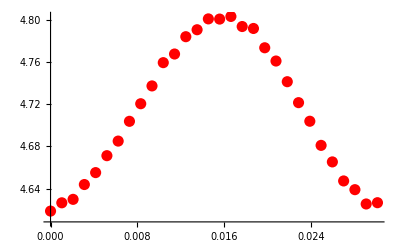

```mathematica
plotnumψ=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```

```mathematica
(*check mu*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/mu_n_12_10.csv"][[2;;]];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{0.0145538,99.898},{0.0166329,101.053},{0.0124747,99.3712},{0.0135143,99.9575},{0.0187121,98.7881},{0.0176725,99.5032},{0.0103956,102.035},{0.0114351,100.743},{0.0207912,97.3447},{0.0197516,101.481},{0.00831647,103.515},{0.00935603,97.5431},{0.0228703,97.3744},{0.0218307,101.513},{0.00623735,101.539},{0.00727691,99.2494},{0.0249494,99.2475},{0.0239098,101.064},{0.00415823,100.964},{0.00519779,100.154},{0.0270285,98.3086},{0.025989,100.666},{0.00207912,100.987},{0.00311868,98.8524},{0.0291076,98.6567},{0.0280681,100.729},{0.0311868,101.408},{0.00103956,99.2579},{0.0301472,100.343}}

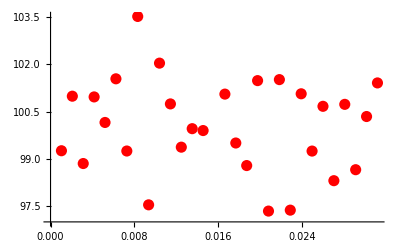

```mathematica
plotnumμ=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```